Articles for comparison:
R&I: https://arxiv.org/pdf/1202.2841.pdf
Dolgov et. al = Dolgov, Hansen, Raffelt, Semikoz: https://arxiv.org/abs/hep-ph/0002223v2 
Mangano et. al: https://arxiv.org/pdf/hep-ph/0506164.pdf
Hannestad&Madsen: https://arxiv.org/pdf/astro-ph/9506015.pdf

```mathematica
Clear["Global`*"];
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/c/Repositories/BBN/pyBBN/src/tests/heavy_sterile_dirac_neutrino

```mathematica
FileToNumLevel2[lines_]:=Module[{func, var, buf},
func = Function[x, var=StringToStream@x;buf=Read[var,Number];Close@var;buf];
Map[func, lines, {2}]
];
```

```mathematica
FileToNumLevel1[lines_]:=Module[{func, var, buf},
func = Function[x, var=StringToStream@x;buf=Read[var,Number];Close@var;buf];
Map[func, lines, {1}]
];
```

```mathematica
Ms=33.9;
```

```mathematica
rawlines03 = Import["./output/0.3/sterile_densities.txt", {"Text", "Lines"}][[2;; ]];
lines03 = StringSplit/@rawlines03;
lines03 = Transpose[FileToNumLevel2[lines03]];
alist03=lines03[[1]];
Tlist03=lines03[[2]];
aTlist03=lines03[[3]];
ρlist03=lines03[[4]];
nlist03=lines03[[5]];
```

```mathematica
rawlines02 = Import["./output/0.2/sterile_densities.txt", {"Text", "Lines"}][[2;; ]];
lines02 = StringSplit/@rawlines02;
lines02 = Transpose[FileToNumLevel2[lines02]];
alist02=lines02[[1]];
ρlist02=lines02[[2]];
nlist02=lines02[[3]];
```

## Comparison with Dolgov, Hansen, Raffelt, Semikoz

```mathematica
ρa03=Interpolation[Transpose[{alist03,ρlist03*alist03^4}],ExtrapolationHandler->{Indeterminate&}] ;
na03=Interpolation[Transpose[{alist03,nlist03*alist03^3}],ExtrapolationHandler->{Indeterminate&}] ;
ρa02=Interpolation[Transpose[{alist02,ρlist02*alist02^4}],ExtrapolationHandler->{Indeterminate&}] ;
na02=Interpolation[Transpose[{alist02,nlist02*alist02^3}],ExtrapolationHandler->{Indeterminate&}] ;
```

```mathematica
ρa03Dolgov=Import["../../figures/Figures-sources/Dolgov_sterile_plots/rhos_tau=0.3.dat","HeaderLines"->1];
ρa03DolgovFunc=Interpolation[ρa03Dolgov[[All,{1,2}]],InterpolationOrder->2,Method->"Spline"];
na03Dolgov=Import["../../figures/Figures-sources/Dolgov_sterile_plots/ns_tau=0.3.dat","HeaderLines"->1];
na03DolgovFunc=Interpolation[na03Dolgov[[All,{1,2}]],InterpolationOrder->2,Method->"Spline"];

ρa02Dolgov=Import["../../figures/Figures-sources/Dolgov_sterile_plots/rhos_tau=0.2.dat","HeaderLines"->1];
ρa02DolgovFunc=Interpolation[ρa02Dolgov[[All,{1,2}]],InterpolationOrder->2,Method->"Spline"];
na02Dolgov=Import["../../figures/Figures-sources/Dolgov_sterile_plots/ns_tau=0.2.dat","HeaderLines"->1];
na02DolgovFunc=Interpolation[na02Dolgov[[All,{1,2}]],InterpolationOrder->2,Method->"Spline"];
```

```mathematica
ρa03[0.05]-ρa03DolgovFunc[0.05]
```

0.194122

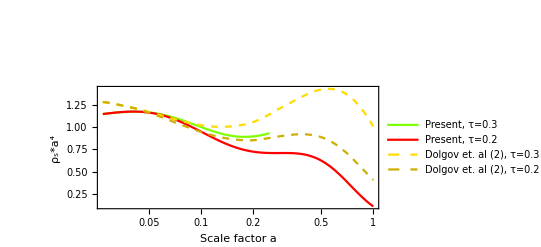

```mathematica
Show[LogLinearPlot[{ρa03[x],ρa02[x],ρa03DolgovFunc[x]+0.2,ρa02DolgovFunc[x]+0.2},{x,0.027,1},PlotRange->All,Frame->True,FrameLabel->{"Scale factor a","ρ_s*a^4"},PlotStyle->{{Thick,Hue[1/4,1,1]},{Thick,Red},{Dashed,Hue[1/7,1,1]},{Dashed,Hue[1/7,1,0.8]}},PlotLegends->{"Present, τ=0.3","Present, τ=0.2","Dolgov et. al (2), τ=0.3","Dolgov et. al (2), τ=0.2"}, Epilog->{Text["KARMEN neutrino
 M_s=33.9MeV",{Log[0.6],3.7}]}]]
Export["rhos_comp_theta0.0486.eps",%];
```

```mathematica
na03[0.07]-na03DolgovFunc[0.07]
```

0.0414085

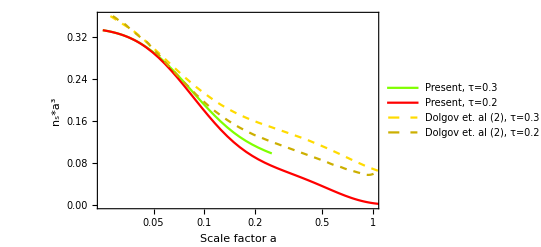

```mathematica
Show[LogLinearPlot[{na03[x],na02[x],na03DolgovFunc[x]+0.05,na02DolgovFunc[x]+0.05},{x,0.025,1.6},PlotRange->{{0.025,1},{0,0.36}},Frame->True,FrameLabel->{"Scale factor a","n_s*a^3"},PlotStyle->{{Thick,Hue[1/4,1,1]},{Thick,Red},{Dashed,Hue[1/7,1,1]},{Dashed,Hue[1/7,1,0.8]}},PlotLegends->{"Present, τ=0.3","Present, τ=0.2","Dolgov et. al (2), τ=0.3","Dolgov et. al (2), τ=0.2"}, Epilog->{Text["KARMEN neutrino
 M_s=33.9MeV",{Log[0.6],3.7}]}]]
Export["ns_comp_theta0.0486.eps",%];
```

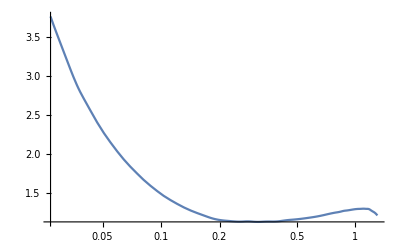

```mathematica
LogLinearPlot[ρa03DolgovFunc[x]/(na03DolgovFunc[x]*x*Ms),{x,0.027,1.3}]
```

### Analytical estimations

```mathematica
feq[p_]:=1/(ⅇ^((√(Ms^2+p^2))/#)+1)&/@Tlist03
```

```mathematica
neq=4*(4 π)/(2 π)^3 NIntegrate[p^2 feq[p],{p,0,∞}];
```

```mathematica
neqa=Interpolation[Transpose[{alist03,neq}]];
```

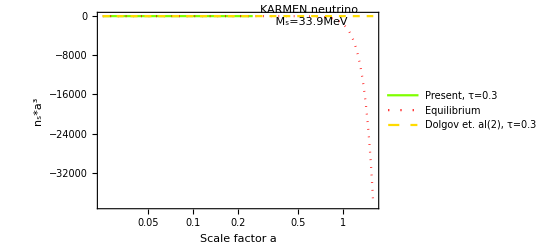

```mathematica
Show[LogLinearPlot[{na03[x],neqa[x]*x^3,na03DolgovFunc[x]},{x,0.025,1.6},PlotRange->All,Frame->True,FrameLabel->{"Scale factor a","n_s*a^3"},PlotStyle->{{Thick,Hue[1/4,1,1]},{Dotted, Red},{Dashed,Hue[1/7,1,1]}},PlotLegends->{"Present, τ=0.3", "Equilibrium","Dolgov et. al(2), τ=0.3"}, Epilog->{Text["KARMEN neutrino
 M_s=33.9MeV",{Log[0.6],3.7}]}]]
Export["ns_tau0.3_plus_analyical.eps",%];
```

```mathematica
ρeq=4*(4 π)/(2 π)^3 NIntegrate[p^2 √(Ms^2+p^2)feq[p],{p,0,∞}];
```

```mathematica
ρeqa=Interpolation[Transpose[{alist03,ρeq}]];
```

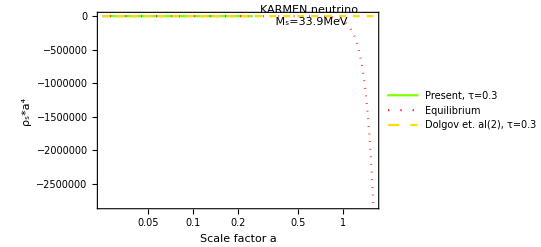

```mathematica
Show[LogLinearPlot[{ρa03[x],ρeqa[x]*x^4,ρa03DolgovFunc[x]},{x,0.025,1.6},PlotRange->All,Frame->True,FrameLabel->{"Scale factor a","ρ_s*a^4"},PlotStyle->{{Thick,Hue[1/4,1,1]},{Dotted, Red},{Dashed,Hue[1/7,1,1]}},PlotLegends->{"Present, τ=0.3", "Equilibrium","Dolgov et. al(2), τ=0.3"}, Epilog->{Text["KARMEN neutrino
 M_s=33.9MeV",{Log[0.6],3.7}]}]]
Export["rhos_tau0.3_plus_analyical.eps",%];
```

## Comparison with Fig. 12 from R&I

```mathematica
ρna=Interpolation[Transpose[{alist03,ρlist03/(nlist03 Ms)}]] ;
```

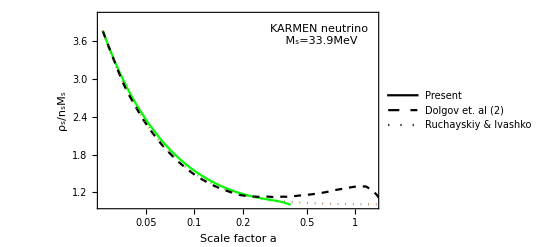

```mathematica
(*rhosns_comp03.eps*)
DolgovTest=Import["../../figures/Figures-sources/rhosns_comp03/03sec_nudec12_x.dat","HeaderLines"->1];
DolgovDigit=Import["../../figures/Figures-sources/rhosns_comp03/ratio_rhos_ns03_semikoz.dat"];
(*Mass of the KARMEN neutrino*)
MKarmen=33.9;
DolgovTestX=DolgovTest[[All,1]];
DolgovTestY=DolgovTest[[All,30]]/DolgovTest[[All,31]]/DolgovTestX/MKarmen;
DolgovTestFunc=Interpolation[Table[Insert[{DolgovTestX[[i]]},DolgovTestY[[i]],2],{i,Length[DolgovTestX]}]];

DolgovDigitFunc=Interpolation[DolgovDigit[[All,{1,2}]]];

Show[LogLinearPlot[{ρna[x],ρa03DolgovFunc[x]/(na03DolgovFunc[x]*x*Ms),DolgovTestFunc[x]},{x,0.027,100},PlotRange->{{0.027,1.3},{1,4}},Frame->True,FrameLabel->{"Scale factor a","ρ_s/n_sM_s"},PlotStyle->{{ Green},{Black, Dashed},{Brown,Dotted}},PlotLegends->LineLegend[{Thick,Dashed, Dotted},{"Present","Dolgov et. al (2)", "Ruchayskiy & Ivashko"}], Epilog->{Text["KARMEN neutrino
 M_s=33.9MeV",{Log[0.6],3.7}]}]]
Export["rhosns_comp03.eps",%];
```